```mathematica
sys={y1'[t]==y1[t-1],
     y2'[t]==y1[t-1]+y2[t-1/5],
     y3'[t]==y2[t],
y1[t/;t<0]==1,y2[t/;t<0]==1,y3[t/;t<0]==1}
```

{y1'[t]==y1[-1+t],y2'[t]==y1[-1+t]+y2[-1/5+t],y3'[t]==y2[t],y1[t/;t<0]==1,y2[t/;t<0]==1,y3[t/;t<0]==1}

```mathematica
solx=DSolve[sys,{y1[t],y2[t],y3[t]},{t,0,5}];
sol=Simplify[solx]
```

{{y1[t]→Piecewise[{{1, t≤0}, {Indeterminate, t>5}, {1+t, 0<t≤1}, {1/2 (3+t^2), 1<t≤2}, {1/6 (1+12 t-3 t^2+t^3), 2<t≤3}, {1/24 (85-60 t+42 t^2-8 t^3+t^4), 3<t≤4}, {1/120 (-599+980 t-430 t^2+120 t^3-15 t^4+t^5), True}}],y2[t]→Piecewise[{{1, t≤0}, {Indeterminate, t>5}, {1+2 t, 0<t≤1/5}, {26/25+(8 t)/5+t^2, 1/5<t≤2/5}, {1/375 (382+660 t+225 t^2+125 t^3), 2/5<t≤3/5}, {(7721+12660 t+5850 t^2+1000 t^3+625 t^4)/7500, 3/5<t≤4/5}, {(192001+322900 t+130250 t^2+45000 t^3+3125 t^4+3125 t^5)/187500, 4/5<t≤1}, {(1717631+793650 t+1390875 t^2+207500 t^3+65625 t^4+3125 t^6)/1125000, 1<t≤6/5}, {(243605489+282271710 t+121195725 t^2+74795000 t^3+6759375 t^4+2362500 t^5-109375 t^6+78125 t^7)/196875000, 6/5<t≤7/5}, {(11010509361+7656426680 t+8788933300 t^2+1036651000 t^3+703543750 t^4+34475000 t^5+17062500 t^6-1250000 t^7+390625 t^8)/7875000000, 7/5<t≤8/5}, {(464372943517+442062175320 t+272654561700 t^2+125001807000 t^3+5453988750 t^4+6117300000 t^5+95812500 t^6+123750000 t^7-10546875 t^8+1953125 t^9)/354375000000, 8/5<t≤9/5}, {(24059153535251+19293672491550 t+17556246271125 t^2+3307908315000 t^3+1538466693750 t^4-6417337500 t^5+50928281250 t^6-646875000 t^7+896484375 t^8-78125000 t^9+9765625 t^10)/17718750000000, 9/5<t≤2}, {1/194906250000000(-194311112239+619477897407050 t-28050041017625 t^2+90940116465000 t^3+5682508631250 t^4+3466596787500 t^5-125570156250 t^6+83118750000 t^7-3029296875 t^8+1289062500 t^9-107421875 t^10+9765625 t^11), 2<t≤11/5}, {1/58471875000000000(57813100565417521+79164318128378340 t+66982597344054150 t^2+1592191015497500 t^3+6585416665059375 t^4+127014225525000 t^5+184436333812500 t^6-10552843125000 t^7+3372380859375 t^8-185195312500 t^9+45761718750 t^10-3515625000 t^11+244140625 t^12), 11/5<t≤12/5}, {1/3800671875000000000(1208131797409159793+10504068982889728740 t-198887302319321850 t^2+2098158023378345500 t^3-59401857115940625 t^4+85441262917725000 t^5-1134528654187500 t^6+1886186176875000 t^7-132122112890625 t^8+27393437500000 t^9-1851738281250 t^10+319921875000 t^11-22216796875 t^12+1220703125 t^13), 12/5<t≤13/5}, {1/266047031250000000000(199755531810208252299+467865895928929679090 t+246306144652072052275 t^2+9833178155393001500 t^3+38152549454706561875 t^4-2044950569242831250 t^5+1031939602490671875 t^6-39422452801875000 t^7+18716079022265625 t^8-1440474191406250 t^9+222888681640625 t^10-16653710937500 t^11+2199462890625 t^12-136718750000 t^13+6103515625 t^14), 13/5<t≤14/5}, {1/19953527343750000000000(9598156695605625910201+48608382040949066782950 t+3871392977755211792625 t^2+9569375674924820072500 t^3-406396933417377459375 t^4+612447891327078056250 t^5-41563583056229609375 t^6+11883627100434375000 t^7-671866885142578125 t^8+181115954550781250 t^9-14451908173828125 t^10+1811291015625000 t^11-139854736328125 t^12+14868164062500 t^13-823974609375 t^14+30517578125 t^15), 14/5<t≤3}, {1/319256437500000000000000(1283366938567708813391341-798878182250576650222800 t+944507880943643935557000 t^2-117180637543488035090000 t^3+53889555846938171587500 t^4-3351018060544094850000 t^5+1793720446735091875000 t^6-135039986412581250000 t^7+26468576798167968750 t^8-1824705762343750000 t^9+342829283671875000 t^10-27405574218750000 t^11+2927729492187500 t^12-223535156250000 t^13+19775390625000 t^14-976562500000 t^15+30517578125 t^16), 3<t≤16/5}, {1/135683985937500000000000000(152794598661936742984894069+290617827871970927591197360 t-15958805464672000587993400 t^2+100414099167760716161310000 t^3-11551322070667230688112500 t^4+4960401112889161999150000 t^5-398732907216324897125000 t^6+122264416286105128750000 t^7-9581712086814613281250 t^8+1435967802890156250000 t^9-109483319559453125000 t^10+15894800157031250000 t^11-1246288278320312500 t^12+117187109375000000 t^13-8595458984375000 t^14+647460937500000 t^15-28533935546875 t^16+762939453125 t^17), 16/5<t≤17/5}, {1/12211558734375000000000000000(40650744701999582505936007219-22140062398887491787391513530 t+35295981282488547763113783825 t^2-6452124280219831366117986000 t^3+3022293118437776813940337500 t^4-302153931983526827477175000 t^5+83192611816422886340062500 t^6-7478213021261109708750000 t^7+1572488716726332203906250 t^8-123855422723448710937500 t^9+15230126249935136718750 t^10-1211110433599218750000 t^11+144585002440429687500 t^12-10971024873046875000 t^13+926385864257812500 t^14-64073730468750000 t^15+4178924560546875 t^16-164794921875000 t^17+3814697265625 t^18), 17/5<t≤18/5}, {1/1160098079765625000000000000000(2019598677103115142945626088173+1521734165507909610161451879930 t+266401464753499557827015300175 t^2+877396868521764957200737698000 t^3-165521326850566237654719457500 t^4+64156118955059743130877975000 t^5-6475793350521250468478062500 t^6+1296232025045741558628750000 t^7-120980660022601141028906250 t^8+19259250606154153460937500 t^9-1493853655971934511718750 t^10+158070696652567968750000 t^11-12628568364940429687500 t^12+1291469753232421875000 t^13-94005041528320312500 t^14+7217346679687500000 t^15-465308074951171875 t^16+26614379882812500 t^17-942230224609375 t^18+19073486328125 t^19), 18/5<t≤19/5}, {1/116009807976562500000000000000000(329261891223373071240165160510401-118164226721386178214543917404900 t+279331372074741518801526823512250 t^2-48838556655132733660311601507500 t^3+30748426183715336665104094528125 t^4-4678804278228556263895414050000 t^5+1217901885798436563140161875000 t^6-120564068873279925872568750000 t^7+18988191368279377274519531250 t^8-1761727259957990636796875000 t^9+226184797775198946835937500 t^10-17073283919545978515625000 t^11+1605823529845012207031250 t^12-125817292507910156250000 t^13+11337037641357421875000 t^14-786933511230468750000 t^15+55358649444580078125 t^16-3304183959960937500 t^17+167427062988281250 t^18-5340576171875000 t^19+95367431640625 t^20), 19/5<t≤4}, {1/2436205967507812500000000000000000(-15660742810387565503956531629281579+27550381024954490257494577734497100 t-11215940406557428105167936706242750 t^2+4651135519273962593133456368342500 t^3-700957368748946680032814014909375 t^4+172316223895748755958196304950000 t^5-21876543479207832174056600625000 t^6+4227662571879871556676056250000 t^7-403485168779804952235089843750 t^8+52710689923206415377265625000 t^9-4734735154533322116445312500 t^10+512194217767659451171875000 t^11-37370589418176618652343750 t^12+3194015507236230468750000 t^13-241690764218994140625000 t^14+19575323998535156250000 t^15-1290427040863037109375 t^16+83579589843750000000 t^17-4601707458496093750 t^18+208282470703125000 t^19-6008148193359375 t^20+95367431640625 t^21), 4<t≤21/5}, {1/1339913282129296875000000000000000000(2240508228001827812349146421439106891-969188976838168658947052330980406310 t+4168799374993354486357283264174765775 t^2-1261438397420738220543968135186967500 t^3+559139547650518190803842247980290625 t^4-86473427012904229480074819807168750 t^5+18545183965468046357251486293328125 t^6-2222335101510768996310555136250000 t^7+340585289869112322114137449218750 t^8-31019632803154375394145742187500 t^9+3485711625214223159500839843750 t^10-298396764144433407542578125000 t^11+28077380310369367027832031250 t^12-1972806301491534448242187500 t^13+155535221934905822753906250 t^14-11259921896518066406250000 t^15+831556181094818115234375 t^16-51907767283630371093750 t^17+3105241832733154296875 t^18-157469558715820312500 t^19+6410694122314453125 t^20-167846679687500000 t^21+2384185791015625 t^22), 21/5<t≤22/5}, {1/154090027444869140625000000000000000000(-765208962483667703777933100875079426383+1558794887702698770560474709866314486510 t-713541309639964509972600203299514966275 t^2+348334013643878143379849396248737649500 t^3-69471327590400931902035771872128978125 t^4+16404324577478196290018974817420393750 t^5-2122776091844133613232393404843265625 t^6+362413806731160865694886457571250000 t^7-40472108309077303925840692539843750 t^8+5150873947890563876957519648437500 t^9-445042011966532699795583417968750 t^10+44129503423644931036453515625000 t^11-3568989996988554027049316406250 t^12+299144538086669449077148437500 t^13-20203269205836931945800781250 t^14+1484302246931254394531250000 t^15-102239024319423065185546875 t^16+6956270000212097167968750 t^17-410318866512298583984375 t^18+22722554779052734375000 t^19-1061171817779541015625 t^20+39087295532226562500 t^21-932216644287109375 t^22+11920928955078125 t^23), 22/5<t≤23/5}, {1/18490803293384296875000000000000000000000(3614261787040018614132785333078394472081+17998689860392705275653730366556642613160 t+47043491356643885885547977643253488467100 t^2-19132422283145635357201497938996019179000 t^3+10013654544796278119004306540667448141250 t^4-1940042942650501429210403137113588525000 t^5+385505812725049208301679048485463187500 t^6-45927460214989074827157632994005625000 t^7+6525568762659051178510682186480859375 t^8-674746157729681852314366265093750000 t^9+73736159483884923815047373671875000 t^10-6024734551442529152963036718750000 t^11+536906325983437465558788085937500 t^12-40855574336954173187753906250000 t^13+3106572403981551706201171875000 t^14-201494892275065828613281250000 t^15+13891005854080937347412109375 t^16-907666759374334716796875000 t^17+57326002093063354492187500 t^18-3190461526336669921875000 t^19+163843374824523925781250 t^20-7052120208740234375000 t^21+236234664916992187500 t^22-5149841308593750000 t^23+59604644775390625 t^24), 23/5<t≤24/5}, {1/2311350411673037109375000000000000000000000(-8432587480804165525393593543984229191240499+19134277210222448189731402315175459472117000 t-8498046229913495119337462643627722205292500 t^2+4856808663262306659470860761661997468225000 t^3-1163410571626122217241459089224125078343750 t^4+324226747194773991868307045454213018375000 t^5-50922804123672284270368614935630701562500 t^6+8171286110300649685804751165093296875000 t^7-897095518369638772811021393569892578125 t^8+109461559071466849923299849663281250000 t^9-10455833043135241286403455891015625000 t^10+1005757525209818437594500410156250000 t^11-77607142589843357735851489257812500 t^12+6300139445892286618343261718750000 t^13-450590237476989676724853515625000 t^14+31524704774096216423339843750000 t^15-1963114579479068378448486328125 t^16+127602629454815826416015625000 t^17-7898798129773330688476562500 t^18+465610664188385009765625000 t^19-24425356375694274902343750 t^20+1164994430541992187500000 t^21-46276330947875976562500 t^22+1416206359863281250000 t^23-28312206268310546875 t^24+298023223876953125 t^25), True}}],y3[t]→Piecewise[{{1, t≤0}, {Indeterminate, t>5}, {1+t+t^2, 0<t≤1/5}, {1/375 (374+390 t+300 t^2+125 t^3), 1/5<t≤2/5}, {(7496+7640 t+6600 t^2+1500 t^3+625 t^4)/7500, 2/5<t≤3/5}, {(187157+193025 t+158250 t^2+48750 t^3+6250 t^4+3125 t^5)/187500, 3/5<t≤4/5}, {(5618806+5760030 t+4843500 t^2+1302500 t^3+337500 t^4+18750 t^5+15625 t^6)/5625000, 4/5<t≤1}, {(32753517+60117085 t+13888875 t^2+16226875 t^3+1815625 t^4+459375 t^5+15625 t^7)/39375000, 1<t≤6/5}, {(7232783016+9744219560 t+5645434200 t^2+1615943000 t^3+747950000 t^4+54075000 t^5+15750000 t^6-625000 t^7+390625 t^8)/7875000000, 6/5<t≤7/5}, {(309552267113+495472921245 t+172269600300 t^2+131833999500 t^3+11662323750 t^4+6331893750 t^5+258562500 t^6+109687500 t^7-7031250 t^8+1953125 t^9)/354375000000, 7/5<t≤8/5}, {(15891563897474+23218647175850 t+11051554383000 t^2+4544242695000 t^3+1562522587500 t^4+54539887500 t^5+50977500000 t^6+684375000 t^7+773437500 t^8-58593750 t^9+9765625 t^10)/17718750000000, 8/5<t≤9/5}, {1/974531250000000(862166785026461+1323253444438805 t+530575993517625 t^2+321864514970625 t^3+45483739331250 t^4+16923133631250 t^5-58825593750 t^6+400150781250 t^7-4447265625 t^8+5478515625 t^9-429687500 t^10+48828125 t^11), 9/5<t≤2}, {1/11694375000000000(18216701420317532-11658666734340 t+18584336922211500 t^2-561000820352500 t^3+1364101746975000 t^4+68190103575000 t^5+34665967875000 t^6-1076315625000 t^7+623390625000 t^8-20195312500 t^9+7734375000 t^10-585937500 t^11+48828125 t^12), 2<t≤11/5}, {1/3800671875000000000(4275476928023066469+3757851536752138865 t+2572840339172296050 t^2+1451289609121173250 t^3+25873104001834375 t^4+85610416645771875 t^5+1375987443187500 t^6+1712623099687500 t^7-85741850390625 t^8+24356083984375 t^9-1203769531250 t^10+270410156250 t^11-19042968750 t^12+1220703125 t^13), 11/5<t≤12/5}, {1/266047031250000000000(370363929363990881694+84569225818641185510 t+367642414401140505900 t^2-4640703720784176500 t^3+36717765409121046250 t^4-831625999623168750 t^5+996814734040125000 t^6-11345286541875000 t^7+16504129047656250 t^8-1027616433593750 t^9+191754062500000 t^10-11783789062500 t^11+1866210937500 t^12-119628906250 t^13+6103515625 t^14), 12/5<t≤13/5}, {1/19953527343750000000000(24579075957574223248793+14981664885765618922425 t+17544971097334862965875 t^2+6157653616301801306875 t^3+184372090413618778125 t^4+572288241820598428125 t^5-25561882115535390625 t^6+11056495740971484375 t^7-369585495017578125 t^8+155967325185546875 t^9-10803556435546875 t^10+1519695556640625 t^11-104085693359375 t^12+12689208984375 t^13-732421875000 t^14+30517578125 t^15), 13/5<t≤14/5}, {1/1596282187500000000000000(2116675192025118459674576+767852535648450072816080 t+1944335281637962671318000 t^2+103237146073472314470000 t^3+191387513498496401450000 t^4-6502350934678039350000 t^5+8165971884361040750000 t^6-475012377785481250000 t^7+118836271004343750000 t^8-5972150090156250000 t^9+1448927636406250000 t^10-105104786718750000 t^11+12075273437500000 t^12-860644531250000 t^13+84960937500000 t^14-4394531250000 t^15+152587890625 t^16), 14/5<t≤3}, {1/27136797187500000000000000(-20447432616469440042954083+109086189778255249138263985 t-33952322745649507634469000 t^2+26761056626736578174115000 t^3-2490088547799120745662500 t^4+916122449397948916987500 t^5-47472755857708010375000 t^6+21780891138926115625000 t^7-1434799855633675781250 t^8+249981003093808593750 t^9-15509998979921875000 t^10+2649135373828125000 t^11-194122817382812500 t^12+19142846679687500 t^13-1357177734375000 t^14+112060546875000 t^15-5187988281250 t^16+152587890625 t^17), 3<t≤16/5}, {1/12211558734375000000000000000(9390395469993355184447076346+13751513879574306868640466210 t+13077802254238691741603881200 t^2-478764163940160017639802000 t^3+2259317231274616113629475000 t^4-207923797272010152386025000 t^5+74406016693337429987250000 t^6-5126565949924177248750000 t^7+1375474683218682698437500 t^8-95817120868146132812500 t^9+12923710226011406250000 t^10-895772614577343750000 t^11+119211001177734375000 t^12-8628149619140625000 t^13+753345703125000000 t^14-51572753906250000 t^15+3641967773437500 t^16-151062011718750 t^17+3814697265625 t^18), 16/5<t≤17/5}, {1/1160098079765625000000000000000(-337367764631700670046205104283+3861820746689960338063920685805 t-1051652963947155859901096892675 t^2+1117706073945470679165269821125 t^3-153237951655220994945302167500 t^4+57423569250317759464866412500 t^5-4784103923072508101721937500 t^6+1129042588937167743186562500 t^7-88803779627475677791406250 t^8+16598492009889062152343750 t^9-1176626515872762753906250 t^10+131532908522167089843750 t^11-9587957599327148437500 t^12+1056582710141601562500 t^13-74446240209960937500 t^14+5867110473632812500 t^15-380437774658203125 t^16+23352813720703125 t^17-869750976562500 t^18+19073486328125 t^19), 17/5<t≤18/5}, {1/116009807976562500000000000000000(48584988418519289087001574409076+201959867710311514294562608817300 t+76086708275395480508072593996500 t^2+8880048825116651927567176672500 t^3+21934921713044123930018442450000 t^4-3310426537011324753094389150000 t^5+1069268649250995718847966250000 t^6-92511333578875006692543750000 t^7+16202900313071769482859375000 t^8-1344229555806679344765625000 t^9+192592506061541534609375000 t^10-13580487781563041015625000 t^11+1317255805438066406250000 t^12-97142833576464843750000 t^13+9224783951660156250000 t^14-626700276855468750000 t^15+45108416748046875000 t^16-2737106323242187500 t^17+147857666015625000 t^18-4959106445312500 t^19+95367431640625 t^20), 18/5<t≤19/5}, {1/12181029837539062500000000000000000(-512128873136345721072702947665939+34572498578454172480217341853592105 t-6203621902872774356263555663757250 t^2+9776598022615953158053438822928750 t^3-1282012112197234258583179539571875 t^4+645716949858022069967185985090625 t^5-81879074868999734618169745875000 t^6+18268528286976548447102428125000 t^7-1582403403961799027077464843750 t^8+221528899296592734869394531250 t^9-18498136229558901686367187500 t^10+2159036706035989947070312500 t^11-149391234296027312011718750 t^12+12970113125671252441406250 t^13-943629693809326171875000 t^14+79359263489501953125000 t^15-5164251167449951171875 t^16+341921070098876953125 t^17-19274406433105468750 t^18+925254821777343750 t^19-28038024902343750 t^20+476837158203125 t^21), 19/5<t≤4}, {1/267982656425859375000000000000000000(1591520883358648394136400535151349342-1722681709142632205435218479220973690 t+1515270956372496964162201775397340500 t^2-411251148240439030522824345895567500 t^3+127906226780033971311170050129418750 t^4-15421062112476826960721908328006250 t^5+3159130771422060525900265590750000 t^6-343774254673265934163746581250000 t^7+58130360363348233904295773437500 t^8-4931485396197616082873320312500 t^9+579817589155270569149921875000 t^10-47347351545333221164453125000 t^11+4695113662870211635742187500 t^12-316212679692263696289062500 t^13+25095836128284667968750000 t^14-1772398937605957031250000 t^15+134580352489929199218750 t^16-8349822029113769531250 t^17+510764160156250000000 t^18-26641464233398437500 t^19+1145553588867187500 t^20-31471252441406250 t^21+476837158203125 t^22), 4<t≤21/5}, {1/154090027444869140625000000000000000000(182330620324891049672499875851581839489+257658446220210198420151838465497292465 t-55728366168194697889455509031373362825 t^2+159803976041411921977029191793366021375 t^3-36266353925846223840639083886625315625 t^4+12860209595961918388488371703546684375 t^5-1657407351080664398368100712970734375 t^6+304670879432689333011988703390390625 t^7-31946067084217304321964230083593750 t^8+4351923148327546338125089628906250 t^9-356725777236275317032676035156250 t^10+36441530627239605758417871093750 t^11-2859635656384153488949707031250 t^12+248376825822498246784667968750 t^13-16205194619394747253417968750 t^14+1192436701500944641113281250 t^15-80930688631223602294921875 t^16+5625232989759063720703125 t^17-331632957645416259765625 t^18+18794884777069091796875 t^19-905449962615966796875 t^20+35106182098388671875 t^21-877380371093750000 t^22+11920928955078125 t^23), 21/5<t≤22/5}, {1/18490803293384296875000000000000000000000(88355099762061385436544074622340843273336-91825075498040124453351972105009531165960 t+93527693262161926233628482591978869190600 t^2-28541652385598580398904008131980598651000 t^3+10450020409316344301395481887462129485000 t^4-1667311862169622365648858524931095475000 t^5+328086491549563925800379496348407875000 t^6-36390447288756576226841029797313125000 t^7+5436207100967412985423296863568750000 t^8-539628110787697385677875900531250000 t^9+61810487374686766523490235781250000 t^10-4855003766907629452315455468750000 t^11+441295034236449310364535156250000 t^12-32944523049125114095839843750000 t^13+2564096040742880992089843750000 t^14-161626153646695455566406250000 t^15+11132266851984407958984375000 t^16-721687230490045166015625000 t^17+46375133334747314453125000 t^18-2591487577972412109375000 t^19+136335328674316406250000 t^20-6063838958740234375000 t^21+213203430175781250000 t^22-4863739013671875000 t^23+59604644775390625 t^24), 22/5<t≤23/5}, {1/2311350411673037109375000000000000000000000(5016064044353844803654493297790205642352057+451782723380002326766598166634799309010125 t+1124918116274544079728358147909790163322500 t^2+1960145473193495245231165735135562019462500 t^3-597888196348301104912546810593625599343750 t^4+250341363619906952975107663516686203531250 t^5-40417561305218779775216732023199760937500 t^6+6884032370090164433958554437240414062500 t^7-717616565859204294174338015531337890625 t^8+90632899481375710812648363701123046875 t^9-8434326971621023153929578313671875000 t^10+837910903225965043352811064453125000 t^11-62757651577526345343364965820312500 t^12+5162560826763821784219116210937500 t^13-364781913722805117747802734375000 t^14+25888103366512930885009765625000 t^15-1574178845898951786041259765625 t^16+102139748927065715789794921875 t^17-6303241384543991088867187500 t^18+377144750612258911132812500 t^19-19940384539604187011718750 t^20+975258183479309082031250 t^21-40068864822387695312500 t^22+1283884048461914062500 t^23-26822090148925781250 t^24+298023223876953125 t^25), 23/5<t≤24/5}, {1/300475553517494824218750000000000000000000000(1201652441974976345277717564604179809447782386-1096236372504541518301167160717949794861264870 t+1243728018664459132332541150486404865687605000 t^2-368248669962918121837956714557201295562675000 t^3+157846281556024966432802974754014917717312500 t^4-30248674862279177648277936319827252036937500 t^5+7024912855886769823813319318174615398125000 t^6-945709219439628136449702848804570171875000 t^7+132783399292385557394327206432766074218750 t^8-12958046376450337829492531240454003906250 t^9+1423000267929069049002898045622656250000 t^10-123568935964325578839313569621093750000 t^11+10895706523106366407273754443359375000 t^12-776071425898433577358514892578125000 t^13+58501294854714090027473144531250000 t^14-3905115391467243864948730468750000 t^15+256138226289531758439636230468750 t^16-15012052666604640541076660156250 t^17+921574546062558746337890625000 t^18-54044408256343841552734375000 t^19+3026469317224502563476562500 t^20-151204587087631225585937500 t^21+6884057998657226562500000 t^22-261561870574951171875000 t^23+7671117782592773437500 t^24-147223472595214843750 t^25+1490116119384765625 t^26), True}}]}}

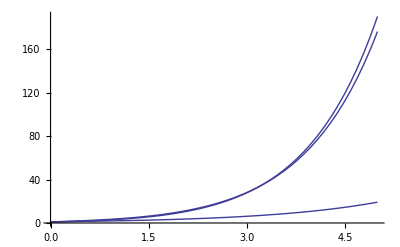

```mathematica
Plot[{y1[t],y2[t],y3[t]}/.sol,{t,0,5},PlotRange->All]
```

```mathematica
Ny={y1[t],y2[t],y3[t]}/.sol/.t->5
```

{{767/40,1372977775497546065372181595185280327502633/7782324618427734375000000000000000000000,2118288127243946981292253783821715691529048793/11128724204351660156250000000000000000000000}}

```mathematica
N[Ny,20]
```

{{19.175,176.4225784473803177,190.34420193607041693}}

```mathematica
y1[t]/.sol//InputForm
```

{Piecewise[{{1, t <= 0}, {Indeterminate, t > 5}, {1 + t, Inequality[0, Less, t, LessEqual, 1]}, 
   {(3 + t^2)/2, Inequality[1, Less, t, LessEqual, 2]}, {(1 + 12*t - 3*t^2 + t^3)/6, Inequality[2, Less, t, LessEqual, 3]}, 
   {(85 - 60*t + 42*t^2 - 8*t^3 + t^4)/24, Inequality[3, Less, t, LessEqual, 4]}}, (-599 + 980*t - 430*t^2 + 120*t^3 - 15*t^4 + t^5)/120]}

```mathematica
tab={Table[First[y1[t]/.sol],{t,5}],
Table[First[y2[t]/.sol],{t,5}],
Table[First[y3[t]/.sol],{t,5}]}
```

{{2,7/2,37/6,87/8,767/40},{696401/187500,187120972422851/17718750000000,11404193203167808022899/407214843750000000000,162019172005425000223647627894251/2274702117187500000000000000000,1372977775497546065372181595185280327502633/7782324618427734375000000000000000000000},{17896711/5625000,9523954835239571/974531250000000,4025234611713839832224131/145116562500000000000000,82125609204103677328910337492038771/1107366348867187500000000000000000,2118288127243946981292253783821715691529048793/11128724204351660156250000000000000000000000}}

```mathematica
N[tab]//TraditionalForm
```

(2. | 3.5 | 6.16667 | 10.875 | 19.175
3.71414 | 10.5606 | 28.0053 | 71.2265 | 176.423
3.18164 | 9.77286 | 27.7379 | 74.163 | 190.344)

```mathematica
tab//TraditionalForm
```

(2 | 7/2 | 37/6 | 87/8 | 767/40
696401/187500 | 187120972422851/17718750000000 | 11404193203167808022899/407214843750000000000 | 162019172005425000223647627894251/2274702117187500000000000000000 | 1372977775497546065372181595185280327502633/7782324618427734375000000000000000000000
17896711/5625000 | 9523954835239571/974531250000000 | 4025234611713839832224131/145116562500000000000000 | 82125609204103677328910337492038771/1107366348867187500000000000000000 | 2118288127243946981292253783821715691529048793/11128724204351660156250000000000000000000000)